```mathematica
(* Mathematica Sheet for Latin Hypercube Sampling for Parental Care*)
(*Making a sheet like the R one where you just have to change values of cf and cm and cfres and cm res*)

(*This defines the number of samples/bins to create*)
n=4000;


(* These next blocks of code define a range for each parameter and using a uniform distribution generate samples within in each bin*)
(*expanding the range of z*)
kmino=0.1;
kmaxo=8;reso=Table[{kmino+(i-1)*(kmaxo-kmino)/n,kmino+i*(kmaxo-kmino)/n,RandomVariate[UniformDistribution[{kmino+(i-1)*(kmaxo-kmino)/(n),kmino+i*(kmaxo-kmino)/(n)}],1]},{i,1,n}];
ao=reso;
z0=RandomSample[Flatten[Table[ao[[i,3]],{i,1,n}],2],n];


kminu=0.01;
kmaxu=0.7;resu=Table[{kminu+(i-1)*(kmaxu-kminu)/n,kminu+i*(kmaxu-kminu)/n,RandomVariate[UniformDistribution[{kminu+(i-1)*(kmaxu-kminu)/(n),kminu+i*(kmaxu-kminu)/(n)}],1]},{i,1,n}];
amu=resu;
cm0=RandomSample[Flatten[Table[amu[[i,3]],{i,1,n}],2],n];



kmink=0.01;
kmaxk=1.0;resk=Table[{kmink+(i-1)*(kmaxk-kmink)/n,kmink+i*(kmaxk-kmink)/n,RandomVariate[UniformDistribution[{kmink+(i-1)*(kmaxk-kmink)/(n),kmink+i*(kmaxk-kmink)/(n)}],1]},{i,1,n}];
ak=resk;
em0=RandomSample[Flatten[Table[ak[[i,3]],{i,1,n}],2],n];


kminx=0.01;
kmaxx=0.7;resx=Table[{kminx+(i-1)*(kmaxx-kminx)/n,kminx+i*(kmaxx-kminx)/n,RandomVariate[UniformDistribution[{kminx+(i-1)*(kmaxx-kminx)/(n),kminx+i*(kmaxx-kminx)/(n)}],1]},{i,1,n}];
ax=resx;
cf0=RandomSample[Flatten[Table[ax[[i,3]],{i,1,n}],2],n];



kmina=0.01;
kmaxa=1.0;resa=Table[{kmina+(i-1)*(kmaxa-kmina)/n,kmina+i*(kmaxa-kmina)/n,RandomVariate[UniformDistribution[{kmina+(i-1)*(kmaxa-kmina)/(n),kmina+i*(kmaxa-kmina)/(n)}],1]},{i,1,n}];
aa=resa;
mum0=RandomSample[Flatten[Table[aa[[i,3]],{i,1,n}],2],n];



kminb=0.01;
kmaxb=1.0;resb=Table[{kminb+(i-1)*(kmaxb-kminb)/n,kminb+i*(kmaxb-kminb)/n,RandomVariate[UniformDistribution[{kminb+(i-1)*(kmaxb-kminb)/(n),kminb+i*(kmaxb-kminb)/(n)}],1]},{i,1,n}];
ab=resb;
muf0=RandomSample[Flatten[Table[ab[[i,3]],{i,1,n}],2],n];



kmind=0.01;
kmaxd=1.0;resd=Table[{kmind+(i-1)*(kmaxd-kmind)/n,kmind+i*(kmaxd-kmind)/n,RandomVariate[UniformDistribution[{kmind+(i-1)*(kmaxd-kmind)/(n),kmind+i*(kmaxd-kmind)/(n)}],1]},{i,1,n}];
ad=resd;
sigjm0=RandomSample[Flatten[Table[ad[[i,3]],{i,1,n}],2],n];


kminh=0.01;
kmaxh=1.0;resh=Table[{kminh+(i-1)*(kmaxh-kminh)/n,kminh+i*(kmaxh-kminh)/n,RandomVariate[UniformDistribution[{kminh+(i-1)*(kmaxh-kminh)/(n),kminh+i*(kmaxh-kminh)/(n)}],1]},{i,1,n}];
ah=resh;
sigjf0=RandomSample[Flatten[Table[ah[[i,3]],{i,1,n}],2],n];



kmini=0.01;
kmaxi=1.0;resi=Table[{kmini+(i-1)*(kmaxi-kmini)/n,kmini+i*(kmaxi-kmini)/n,RandomVariate[UniformDistribution[{kmini+(i-1)*(kmaxi-kmini)/(n),kmini+i*(kmaxi-kmini)/(n)}],1]},{i,1,n}];
ai=resi;
taum0=RandomSample[Flatten[Table[ai[[i,3]],{i,1,n}],2],n];


kminj=0.01;
kmaxj=1.0;resj=Table[{kminj+(i-1)*(kmaxj-kminj)/n,kminj+i*(kmaxj-kminj)/n,RandomVariate[UniformDistribution[{kminj+(i-1)*(kmaxj-kminj)/(n),kminj+i*(kmaxj-kminj)/(n)}],1]},{i,1,n}];
aj=resj;
tauf0=RandomSample[Flatten[Table[aj[[i,3]],{i,1,n}],2],n];


kminz=0.01;
kmaxz=1.0;resz=Table[{kminz+(i-1)*(kmaxz-kminz)/n,kminz+i*(kmaxz-kminz)/n,RandomVariate[UniformDistribution[{kminz+(i-1)*(kmaxz-kminz)/(n),kminz+i*(kmaxz-kminz)/(n)}],1]},{i,1,n}];
zz=resz;
mm0=RandomSample[Flatten[Table[zz[[i,3]],{i,1,n}],2],n];



kminy=0.01;
kmaxy=1.0;resy=Table[{kminy+(i-1)*(kmaxy-kminy)/n,kminy+i*(kmaxy-kminy)/n,RandomVariate[UniformDistribution[{kminy+(i-1)*(kmaxy-kminy)/(n),kminy+i*(kmaxy-kminy)/(n)}],1]},{i,1,n}];
yy=resy;

mf0=RandomSample[Flatten[Table[yy[[i,3]],{i,1,n}],2],n];



kminc=50;
kmaxc=250;resc=Table[{kminc+(i-1)*(kmaxc-kminc)/n,kminc+i*(kmaxc-kminc)/n,RandomVariate[UniformDistribution[{kminc+(i-1)*(kmaxc-kminc)/(n),kminc+i*(kmaxc-kminc)/(n)}],1]},{i,1,n}];
ac=resc;

k0=RandomSample[Flatten[Table[ac[[i,3]],{i,1,n}],2],n];



kminx=2;
kmaxx=8;resx=Table[{kminx+(i-1)*(kmaxx-kminx)/n,kminx+i*(kmaxx-kminx)/n,RandomVariate[UniformDistribution[{kminx+(i-1)*(kmaxx-kminx)/(n),kminx+i*(kmaxx-kminx)/(n)}],1]},{i,1,n}];
ax=resx;

rr0=RandomSample[Flatten[Table[ax[[i,3]],{i,1,n}],2],n];



kmine=0.01;
kmaxe=1.0;rese=Table[{kmine+(i-1)*(kmaxe-kmine)/n,kmine+i*(kmaxe-kmine)/n,RandomVariate[UniformDistribution[{kmine+(i-1)*(kmaxe-kmine)/(n),kmine+i*(kmaxe-kmine)/(n)}],1]},{i,1,n}];
ae=rese;
wm0=RandomSample[Flatten[Table[ae[[i,3]],{i,1,n}],2],n];


kming=0.01;
kmaxg=1.0;resg=Table[{kming+(i-1)*(kmaxg-kming)/n,kming+i*(kmaxg-kming)/n,RandomVariate[UniformDistribution[{kming+(i-1)*(kmaxg-kming)/(n),kming+i*(kmaxg-kming)/(n)}],1]},{i,1,n}];
ag=resg;
wf0=RandomSample[Flatten[Table[ag[[i,3]],{i,1,n}],2],n];




(*Mutant*)
z=1;

(*cm=cm0;
cf=0.7-cm0;*)
cm=0.6;
cf=0.0;
ct = cm + cf;
ct;

(*em=em0;*)
em=em0;
ef = 1-em;

mum=mum0*E^(-z*ct);
muf=muf0*E^(-z*ct);

sigjm=sigjm0;
sigjf=sigjf0;

taum =taum0;
tauf=tauf0;

mm=1-((1-mm0)*E^(-((1-mum0)*em)));
mf=1-((1-mf0)*E^(-((1-muf0)*ef)));

k=k0;

rr=rr0*E^(-((1-mum0)*em+((1-muf0)*ef))/2);
(*added r and maturation rate edits/ trade-off*)

wm=1-((1-wm0)*E^(-cm));
wf= 1- ((1-wf0)*E^(-(ef*(1-muf0)+(1-mum0)*em +cf)));


emm = em*(1-mum)*mm;
emf = ef* (1-muf)*mf;
esm = em*(1-mum);
esf = ef*(1-muf);

am = em*(1-mum)*mm*sigjm;
af = ef* (1-muf)* mf*sigjf;




(*Resident*)

(*emres =em0; *)
emres=em0;
efres =1-emres;

zres =1;
cmres = 0.0;
cfres = 0.0;
ctres = cmres+cfres;

mumres=mum0*E^(-zres*ctres);
mufres=muf0*E^(-zres*ctres);

sigjmres=sigjm0;
sigjfres=sigjf0;

taumres=taum0;
taufres =tauf0;

mmres=1-((1-mm0)*E^(-((1-mum0)*emres)));
mfres=1-((1-mf0)*E^(-((1-muf0)*efres)));

KR=k0;
rres=rr0*E^(-((1-mum0)*emres+((1-muf0)*efres))/2);

wmres=1-(1-wm0)*E^(-cmres);
wfres= 1- (1-wf0)*E^(-(efres*(1-muf0)+(1-mum0)*emres+cfres));


emmres = emres*(1-mumres)*mmres;
emfres = efres* (1-mufres)*mfres;
esmres= emres*(1-mumres);
esfres = efres* (1-mufres);
amres = emres*(1-mumres)*mmres*sigjmres;
afres = efres* (1-mufres)* mfres*sigjfres;




AR =KR*(1-((wmres*amres+wfres*afres)*(mumres*emres + mufres*efres + mmres*esmres + mfres*esfres)/((emmres*sigjmres+emfres*sigjfres)*rres*afres)));
```

```mathematica
(*Invading male only care (cm = x axis, cf=0.0 ) into female only care (cm= 0.0, cf= 0.7)*)
```

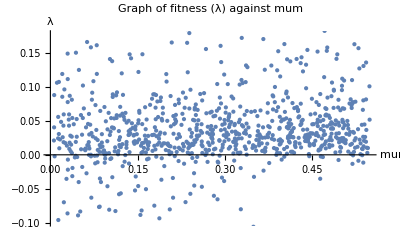

0.173533

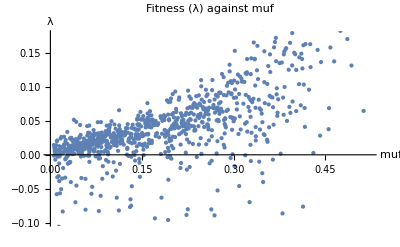

0.628422

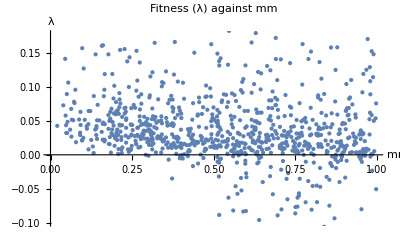

-0.227943

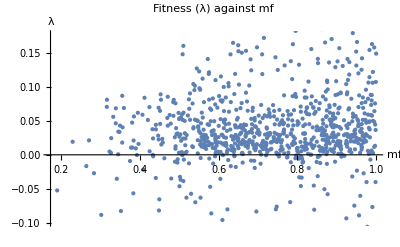

0.112786

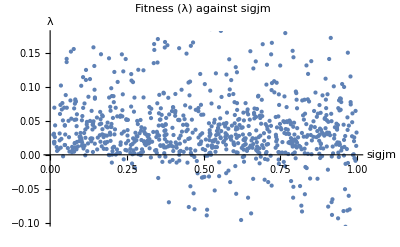

-0.127121

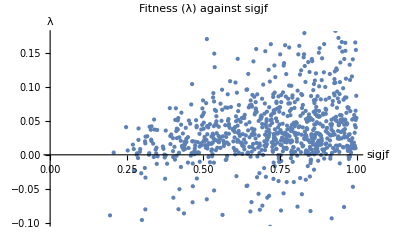

0.318335

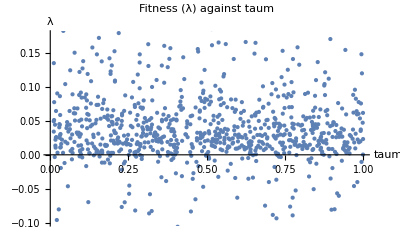

-0.0122377

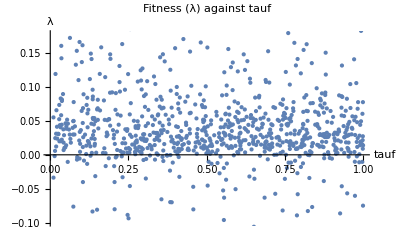

-0.0602872

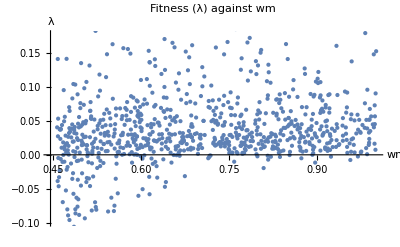

0.230769

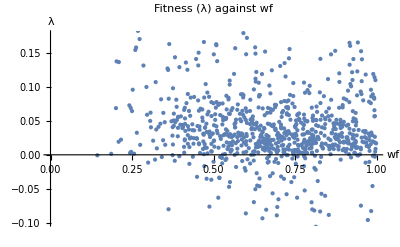

-0.148135

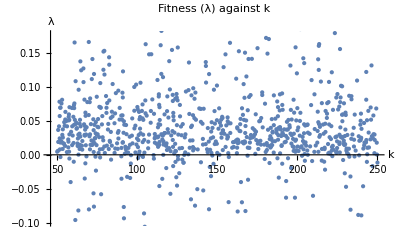

-0.0626026

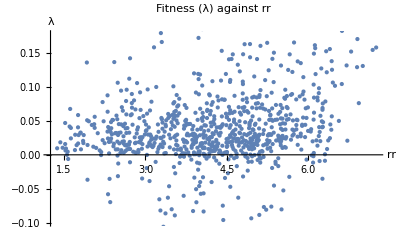

0.228772

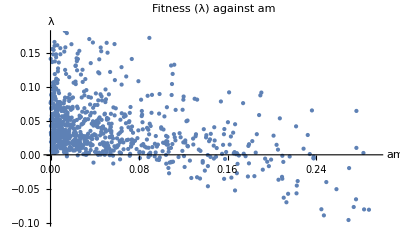

-0.571578

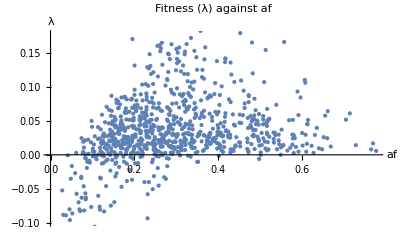

0.283628

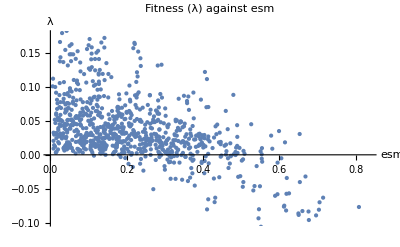

-0.55556

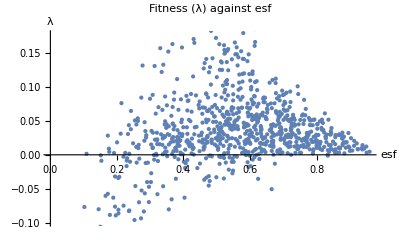

0.155403

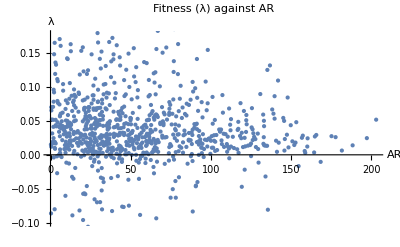

-0.110274

Part::partd: Part specification 0.6⟦4⟧ is longer than depth of object.

Part::partd: Part specification 0.6⟦15⟧ is longer than depth of object.

Part::partd: Part specification 0.6⟦16⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

Part::partd: Part specification 1⟦4⟧ is longer than depth of object.

Part::partd: Part specification 1⟦15⟧ is longer than depth of object.

Part::partd: Part specification 1⟦16⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification 1.⟦4⟧ is longer than depth of object.

Part::partd: Part specification 1.⟦15⟧ is longer than depth of object.

Part::partd: Part specification 1.⟦16⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

Part::partd: Part specification 1.⟦4⟧ is longer than depth of object.

Part::partd: Part specification 1.⟦15⟧ is longer than depth of object.

Part::partd: Part specification 1.⟦16⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Parameter | Correlation
mum | 0.1735
muf | 0.6284
mm | -0.2279
mf | 0.1128
sigjm | -0.1271
sigjf | 0.3183
taum | -0.0122
tauf | -0.0603
wm | 0.2308
wf | -0.1481
k | -0.0626
rr | 0.2288
am | -0.5716
af | 0.2836
esm | -0.5556
esf | 0.1554
AR | -0.1103

```mathematica
res2hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{mum[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res2hpm2 = Select[res2hpm2, # =!= Nothing &];
ListPlot[res2hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Graph of fitness (λ) against mum",
AxesLabel ->{"mum", "λ"}]
column1=res2hpm2[[All, 1]];
column2 = res2hpm2[[All,2]];
correlationcoefficientmum =Correlation[column1,column2];
correlationcoefficientmum

res3hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{muf[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res3hpm2 = Select[res3hpm2, # =!= Nothing &];
ListPlot[res3hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against muf",
AxesLabel ->{"muf", "λ"}]
column1=res3hpm2[[All, 1]];
column2 = res3hpm2[[All,2]];
correlationcoefficientmuf =Correlation[column1,column2];
correlationcoefficientmuf

res19hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{mm[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res19hpm2 = Select[res19hpm2, # =!= Nothing &];


ListPlot[res19hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against mm",
AxesLabel ->{"mm", "λ"}]
column1=res19hpm2[[All, 1]];
column2 = res19hpm2[[All,2]];
correlationcoefficientmm =Correlation[column1,column2];
correlationcoefficientmm 

res20hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{mf[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res20hpm2 = Select[res20hpm2, # =!= Nothing &];
ListPlot[res20hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against mf",
AxesLabel ->{"mf", "λ"}]
column1=res20hpm2[[All, 1]];
column2 = res20hpm2[[All,2]];
correlationcoefficientmf =Correlation[column1,column2];
correlationcoefficientmf


res4hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{sigjm[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res4hpm2 = Select[res4hpm2, # =!= Nothing &];
ListPlot[res4hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against sigjm",
AxesLabel ->{"sigjm", "λ"}]
column1=res4hpm2[[All, 1]];
column2 = res4hpm2[[All,2]];
correlationcoefficientsigjm =Correlation[column1,column2];
correlationcoefficientsigjm

res5hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{sigjf[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res5hpm2 = Select[res5hpm2, # =!= Nothing &];
ListPlot[res5hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against sigjf",
AxesLabel ->{"sigjf", "λ"}]
column1=res5hpm2[[All, 1]];
column2 = res5hpm2[[All,2]];
correlationcoefficientsigjf=Correlation[column1,column2];
correlationcoefficientsigjf


res6hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{taum[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res6hpm2 = Select[res6hpm2, # =!= Nothing &];
ListPlot[res6hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against taum",
AxesLabel ->{"taum", "λ"}]
column1=res6hpm2[[All, 1]];
column2 = res6hpm2[[All,2]];
correlationcoefficienttaum =Correlation[column1,column2];
correlationcoefficienttaum

res7hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{tauf[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res7hpm2 = Select[res7hpm2, # =!= Nothing &];
ListPlot[res7hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against tauf",
AxesLabel ->{"tauf", "λ"}]
column1=res7hpm2[[All, 1]];
column2 = res7hpm2[[All,2]];
correlationcoefficienttauf =Correlation[column1,column2];
correlationcoefficienttauf

res8hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{wm[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res8hpm2 = Select[res8hpm2, # =!= Nothing &];
ListPlot[res8hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against wm",
AxesLabel ->{"wm", "λ"}]
column1=res8hpm2[[All, 1]];
column2 = res8hpm2[[All,2]];
correlationcoefficientwm =Correlation[column1,column2];
correlationcoefficientwm

res9hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{wf[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res9hpm2 = Select[res9hpm2, # =!= Nothing &];
ListPlot[res9hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against wf",
AxesLabel ->{"wf", "λ"}]
column1=res9hpm2[[All, 1]];
column2 = res9hpm2[[All,2]];
correlationcoefficientwf =Correlation[column1,column2];
correlationcoefficientwf

res10hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{k[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res10hpm2 = Select[res10hpm2, # =!= Nothing &];
ListPlot[res10hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against k",
AxesLabel ->{"k", "λ"}]
column1=res10hpm2[[All, 1]];
column2 = res10hpm2[[All,2]];
correlationcoefficientk =Correlation[column1,column2];
correlationcoefficientk

res11hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{rr[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res11hpm2 = Select[res11hpm2, # =!= Nothing &];
ListPlot[res11hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against rr",
AxesLabel ->{"rr", "λ"}]
column1=res11hpm2[[All, 1]];
column2 = res11hpm2[[All,2]];
correlationcoefficientrr =Correlation[column1,column2];
correlationcoefficientrr


res12hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{am[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res12hpm2 = Select[res12hpm2, # =!= Nothing &];
ListPlot[res12hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against am",
AxesLabel ->{"am", "λ"}]
column1=res12hpm2[[All, 1]];
column2 = res12hpm2[[All,2]];
correlationcoefficientam =Correlation[column1,column2];
correlationcoefficientam


res13hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{af[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res13hpm2 = Select[res13hpm2, # =!= Nothing &];
ListPlot[res13hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against af",
AxesLabel ->{"af", "λ"}]
column1=res13hpm2[[All, 1]];
column2 = res13hpm2[[All,2]];
correlationcoefficientaf =Correlation[column1,column2];
correlationcoefficientaf

res14hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{esm[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res14hpm2 = Select[res14hpm2, # =!= Nothing &];
ListPlot[res14hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against esm",
AxesLabel ->{"esm", "λ"}]
column1=res14hpm2[[All, 1]];
column2 = res14hpm2[[All,2]];
correlationcoefficientesm =Correlation[column1,column2];
correlationcoefficientesm

res15hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{esf[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res15hpm2 = Select[res15hpm2, # =!= Nothing &];
ListPlot[res15hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against esf",
AxesLabel ->{"esf", "λ"}]
column1=res15hpm2[[All, 1]];
column2 = res15hpm2[[All,2]];
correlationcoefficientesf =Correlation[column1,column2];
correlationcoefficientesf



res16hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{AR[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res16hpm2 = Select[res16hpm2, # =!= Nothing &];
ListPlot[res16hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against AR",
AxesLabel ->{"AR", "λ"}]
column1=res16hpm2[[All, 1]];
column2 = res16hpm2[[All,2]];
correlationcoefficientAR =Correlation[column1,column2];
correlationcoefficientAR

res17hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{cm[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res17hpm2 = Select[res17hpm2, # =!= Nothing &];
ListPlot[res17hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Graph of fitness (λ) against cm",
AxesLabel ->{"cm", "λ"}]
column1=res17hpm2[[All, 1]];
column2 = res17hpm2[[All,2]];
correlationcoefficientcm =Correlation[column1,column2];
correlationcoefficientcm

res18hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{z[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res18hpm2 = Select[res18hpm2, # =!= Nothing &];
ListPlot[res18hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Graph of fitness (λ) against z",
AxesLabel ->{"z", "λ"}]
column1=res18hpm2[[All, 1]];
column2 = res18hpm2[[All,2]];
correlationcoefficientz =Correlation[column1,column2];
correlationcoefficientz



coefTable={{"mum",correlationcoefficientmum}, {"muf",correlationcoefficientmuf},{"mm", correlationcoefficientmm},{"mf", correlationcoefficientmf}, {"sigjm", correlationcoefficientsigjm}, {"sigjf", correlationcoefficientsigjf}, {"taum", correlationcoefficienttaum}, {"tauf", correlationcoefficienttauf},{"wm", correlationcoefficientwm}, {"wf", correlationcoefficientwf}, {"k", correlationcoefficientk}, {"rr", correlationcoefficientrr}, {"am", correlationcoefficientam}, {"af", correlationcoefficientaf}, {"esm", correlationcoefficientesm}, {"esf", correlationcoefficientesf}, {"AR", correlationcoefficientAR}};

formattedTable = MapAt[
If[NumericQ@#, NumberForm[#,{5,4}],#]&,
coefTable,
{All,2}
];
Grid[Prepend[formattedTable,{"Parameter","Correlation"}],
 Frame ->All, 
Alignment -> {"."},
Dividers-> {{2->True}, {2->True}}
]
```